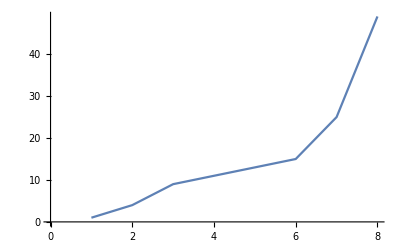

```mathematica
ListLinePlot[{1,4,9,11,13,15,25,49}]
```

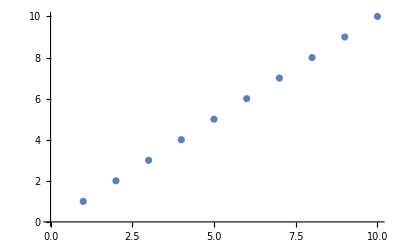

```mathematica
ListPlot[{Range[10]}]
```

```mathematica
Reverse[Range[20]]
```

{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

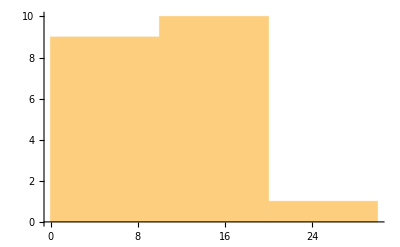

```mathematica
Histogram[{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}]
```

```mathematica
Join[{1,2,3},{456}]
```

{1,2,3,456}

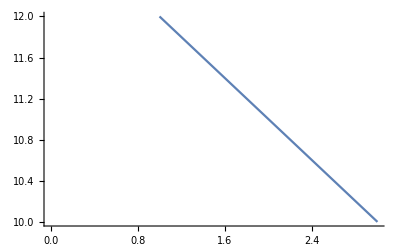

```mathematica
ListLinePlot[Reverse[Range[10,12]]]
```

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

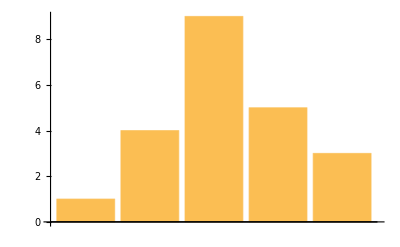

```mathematica
BarChart[{1,4,9,5,3}]
```

```mathematica
PieChart3D[{2,4,5,10}]
```

-Graphics3D-

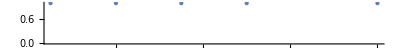

```mathematica
NumberLinePlot[{1,4,7,10,16}]
```

```mathematica
Column[{100,120,115,240,260}]
```

100
120
115
240
260

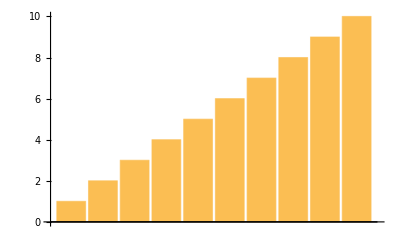
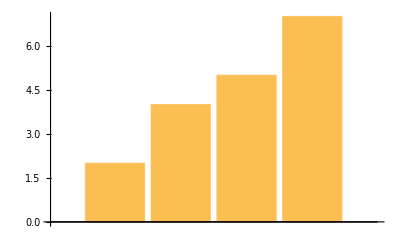
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
{BarChart[Range[10]],BarChart[{2,4,5,7}],BarChart3D[{1,5,2,8}]}
```

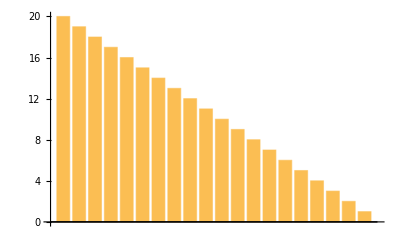

```mathematica
BarChart[Reverse[Range[20]]]
```

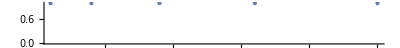

```mathematica
NumberLinePlot[{1,2,3,4,5}^2]
```

```mathematica
Column[{PieChart[{1,2,3}],PieChart[{5,6,8}]}]
```

-Graphics-

```mathematica
{Red,Green,Blue}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

```mathematica
Graphics3D[PlanetData[PlanetData[],"OrbitPath"]]
```

-Graphics3D-

```mathematica
MannedSpaceMissionData["SampleEntities"]
```

{Apollo 1,Apollo 12,Apollo 14,Apollo 16,Mercury-Redstone 3,Soyuz 37,Soyuz-TMA 3,STS 129,STS 5,STS 51L}

```mathematica
ents=EntityList[EntityClass["MannedSpaceMission","ApolloMannedMission"]];
```

```mathematica
GeoListPlot[ents,GeoRange->All,GeoProjection->"Orthographic",GeoLabels->True,LabelStyle->White]
```

-Graphics-

```mathematica
CovarianceFunction[WienerProcess[μ,σ],s,t]
```

σ^2 Min[s,t]

```mathematica
CovarianceFunction[WienerProcess[μ,σ],s,t];
Plot3D[Evaluate[%/.{μ->1,σ->2}],{s,0,10},{t,0,10},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Module[{i,x,y,s,m=0,n=200000},For[i=n,i>0,i=i-1,x=Random[];y=Random[];s=If[x^2+y^2≤1,1,0];m=m+s];
N[4 m/n]]
```

3.13846